```mathematica
Subscript[k, 0]=20;
Subscript[X, 0]=-5;
Subscript[X, d]=-3;
δ=0.5;
Subscript[δ, 1]=0.005;

n=4;
m=100;
Ti=-0.02;
Tf=0.22;
dt=(Tf-Ti)/(m-1);

tm[0]=Ti-dt;
tm[1]=Ti;
tm[m+1]=Tf+dt;

Do[tm[i]=tm[i-1]+dt,{i,2,m}]

ψ[0,x_,t_]:=(δ^2/(2π))^(1/4)*Exp[-Subscript[k, 0]^2*δ^2]/(√(δ^2+(ⅈ*t)/2))*Exp[((2*δ^2* Subscript[k, 0] + ⅈ*(x-Subscript[X, 0]))^2)/(4*δ^2 + 2*ⅈ*t)]
K[xf_,tf_,xi_,ti_]:=1/(√(2*π*ⅈ*(tf-ti)))*Exp[(ⅈ*(xf-xi)^2)/(2*(tf-ti))]

a[1]=Abs[ψ[0,Subscript[X, d],Tm[1]]]*Sqrt[Subscript[δ, 1]];
b[1]=√(1-(a[1])^2);

Do[α[0,j]=ψ[0,Subscript[X, d],Tm[j]],{j,1,n+1}]

Do[Do[β[i,j]=K[Subscript[X, d],0,Subscript[X, d],Tm[j]-Tm[i]],{j,i+1,n+1}],{i,1,n}]
```

```mathematica
list={};Do[list=Append[list,tm[i]],{i,1,m}];TList=Tuples[list,{n}];
```

```mathematica
Length[TList]
```

100000000

```mathematica
TList[[5000]][[1]]
```

-0.02

```mathematica
TList[[7000]]
```

{0.0333333,0.06,0.193333,0.14,0.113333}

```mathematica
Do[Tm[j]=TList[[14000]][[j]],{j,1,n}]
```

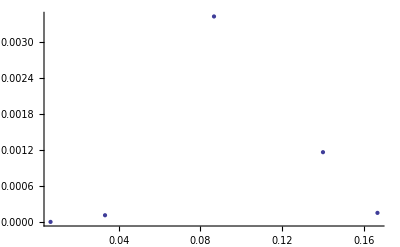

0.100713

```mathematica
ListPlot[Table[{Tm[i],(a[i])^2},{i,n}],PlotRange->All]
top=(∑_(j=1)^n Tm[j]*(Abs[α[0,j]])^2*Subscript[δ, 1])/(∑_(j=1)^n (Abs[α[0,j]])^2*Subscript[δ, 1])
```

```mathematica
Do[{Do[Tm[j]=TList[[i]][[j]],{j,1,n}]; Do[Do[If[Tm[i]≠Tm[j],{α[i,j]=(α[i-1,j]-α[i-1,i]*β[i,j]*Subscript[δ, 1])/b[i]},{α[i,j]=0}],{j,i+1,n+1}];a[i+1]=Abs[α[i,i+1]]*Sqrt[Subscript[δ, 1]];b[i+1]=√(1-(a[i+1])^2),{i,1,n}];Do[prob[i,j]=(∏_(k=1)^(j-1) b[k]^2)*(a[j])^2,{j,2,n,1}];
prob[i,1]=(a[1])^2  },{i,1,Length[TList]}];tbar=(∑_(i=1)^Length[TList] ∑_(j=1)^n (TList[[i]][[j]]*prob[i,j]))/(∑_(i=1)^Length[TList] ∑_(j=1)^n prob[i,j])
```

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

```mathematica
prob[5040,3]
```

0.00380109

```mathematica
tbar=(∑_(i=1)^Length[TList] ∑_(j=1)^n (TList[[i]][[j]]*prob[i,j]))/(∑_(i=1)^Length[TList] ∑_(j=1)^n prob[i,j])
```

$Aborted

```mathematica
0.10050713826340517
```

0.100507

```mathematica
.1-{{%}, {□}}
```

-0.000507138

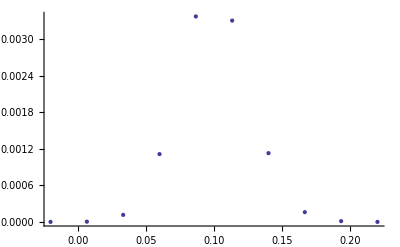

```mathematica
Do[prob[i_]:=(∏_(k=1)^(i-1) b[k]^2)*(a[i])^2,{i,2,n,1}]
prob[1]=(a[1])^2;

ListPlot[Table[{tm[i],prob[i]},{i,n}],PlotRange->All]

tbar=(∑_(j=1)^n (tm[j]*prob[j]))/(∑_(j=1)^n prob[j])
```

```mathematica
A={1,2,3}
```

{1,2,3}

```mathematica
Subsets[A,{2}]
```

{{1,2},{1,3},{2,3}}

```mathematica
Permutations[A,{2}]
```

{{1,2},{1,3},{2,1},{2,3},{3,1},{3,2}}

```mathematica
Tuples[A,{3}]
```

{{1,1,1},{1,1,2},{1,1,3},{1,2,1},{1,2,2},{1,2,3},{1,3,1},{1,3,2},{1,3,3},{2,1,1},{2,1,2},{2,1,3},{2,2,1},{2,2,2},{2,2,3},{2,3,1},{2,3,2},{2,3,3},{3,1,1},{3,1,2},{3,1,3},{3,2,1},{3,2,2},{3,2,3},{3,3,1},{3,3,2},{3,3,3}}

```mathematica
?Tuples
```

Tuples[list,n] generates a list of all possible n-tuples of elements from list. 
Tuples[{list_1,list_2,…}] generates a list of all possible tuples whose i^th element is from list_i.

```mathematica
Length[%]
```

27